```mathematica
Needs["VariationalMethods`"]
Quit;
ClearAll;
```

```mathematica
L=1;
```

```mathematica
Action=Sqrt[r[x]^2(r[x]^2+2r'[x]v'[x]-(r[x]^2-m[v[x]]/r[x])v'[x]^2)]; (*Action functional (eqn4.5)*)
```

```mathematica
FullSimplify[Eliminate[{EulerEquations[Action,v[x],x],EulerEquations[Action,r[x],x],r[x]^6/r0^4==r[x]^2+2 r'[x] v'[x]-((-m[v[x]])/r[x]+r[x]^2) v'[x]^2},m[v[x]]]] (*We can eliminate one of the two EL equaitons using eqn4.6 which can be derived from reparametrrising the action in terms of v and then minimising*)
```

r[x]^11/r0^8+3 r[x]^3 (-1+v'[x]^2)+(-4 r'[x]^2 v'[x]^2+m'[v[x]] v'[x]^4)/r[x]+2 v'[x]^2 r''[x]==(-2 r[x]^7+2 r[x] (3 r0^4+r[x]^4) r'[x] v'[x]+3 r[x]^7 v'[x]^2)/r0^4&&3 r[x]+r[x]^5/r0^4+(6 r'[x] v'[x])/r[x]==3 r[x] v'[x]^2+2 v''[x]

```mathematica
a=1/3; (*Parameter which controls the speed of the perturbation*)
Subscript[m, 0]=1; (*final value of mass function*)
m[v_]:=Subscript[m, 0](Tanh[v/a]+1)/2; (*define the mass function*)
t=6; (*Inital field theory time on boundary*)
rmax=100;
xmax=100;
```

NDSolve::ndsz: At x == 7.00632, step size is effectively zero; singularity or stiff system suspected.

{{r→                                  -8
InterpolatingFunction[{{5.33333 10  , 7.00632}}, <>],v→                                  -8
InterpolatingFunction[{{5.33333 10  , 7.00632}}, <>]}}

rmin= -6.37201×10^44

vmin= -1.27719×10^69

ℓ/2= 100.

x @ vmin 100.

x @ rmin 81.8088

InterpolatingFunction::dmval: Input value {100.} lies outside the range of data in the interpolating function. Extrapolation will be used.

derivatives @ ℓ/2{{1.58075×10^44,-6.86709×10^67}}

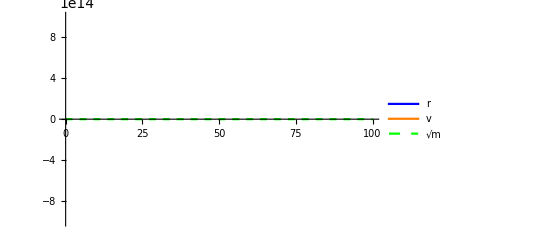

```mathematica
r0=0.4; (*Minimum value of r*)
Eqn1=r0^4(r[x]^2+2r'[x]v'[x]-(r[x]^2-m[v[x]]/r[x])v'[x]^2)-r[x]^6; (*the two equations of motion eqns 4.6, 4.7*)
Eqn2=3 r[x]+r[x]^5/r0^4+(6 r'[x] v'[x])/r[x]-3 r[x] v'[x]^2-2 v''[x];
x0=1/3 r0^2/rmax^3;
b=0.635802198662;(*integration const b*)
Sol=NDSolve[{Eqn1==0,Eqn2==0,r[x0]==rmax,v[x0]==t-1/rmax,v'[x0]==-rmax^2/r0^2+b/r0^2},{r,v},{x,x0,xmax}]
ℓ=2*x/.Last[Quiet[FindMinimum[v[x]/.Sol,{x,x0,x0,xmax}]]];
Print["rmin= ",rmin=First[Quiet[FindMinimum[r[x]/.Sol,{x,ℓ/2,x0,ℓ/2}]]]]
Print["vmin= ",vmin=First[Quiet[FindMinimum[v[x]/.Sol,{x,ℓ/2,x0,ℓ/2}]]]]
Print["ℓ/2= ",ℓ/2]
Print["x @ vmin ",x/.Last[Quiet[FindMinimum[v[x]/.Sol,{x,ℓ/2,x0,ℓ/2}]]]]
Print["x @ rmin ",x/.Last[Quiet[FindMinimum[r[x]/.Sol,{x,ℓ/2,x0,ℓ/2}]]]]
Print["derivatives @ ℓ/2",{r'[ℓ/2-x0],v'[ℓ/2]}/.Sol]
ab=Plot[{Evaluate[r[x]/.Sol],Evaluate[v[x]/.Sol],Evaluate[m[v[x]]^(1/3)/.Sol]},{x,x0,ℓ/2},PlotStyle->{Blue,Orange,{Dashed,Green}},PlotLegends->{"r","v","√m"},AxesOrigin->{0,0}]
```

```mathematica
LInt=2/r0^2*(NIntegrate[r[x]^4/.Sol,{x,x0,ℓ/2}])-2rmax
ℓ
```

{8.41861}

11.4056

```mathematica
abc=ListCurvePathPlot[{{0.406622,-3.4889567476347167},{0.623559,-2.19713},{1.36947,-0.58012},{2.9638,1.19304},{10.24,8.39704},{11.4056,8.41861},{14.6727,8.46855},{30,8.5}},InterpolationOrder->2]
```

-Graphics-

```mathematica
~
```

```mathematica
Show[{VacRes,TherRes,abc},PlotRange->{{0,20},{-10,20}},AxesLabel->{"ℓ","Ã(ℓ,t)"},AspectRatio->1,PlotRange->All]
```

-Graphics-

```mathematica
~
```

```mathematica
ac=ParametricPlot3D[{Evaluate[{x,v[x],r[x]}/.Sol]},{x,x0,ℓ/2},AxesLabel->{"x","v","r"},PlotRange->{{x0,ℓ/2},{-8,t},{0.0,2.0}}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[Evaluate[{y,x,r[x]}/.Sol],{x,x0,ℓ/2},{y,x0,10}] (*plot of surface need to reflect *)
```

-Graphics3D-

```mathematica
pq=ParametricPlot3D[Evaluate[{y,v[x],m[v[x]]^(1/3)}/.Sol],{x,x0,ℓ/2},{y,x0,ℓ/2},PlotRange->All]
```

-Graphics3D-

```mathematica
f=Show[{ac,pq},AspectRatio->1/2]
```

-Graphics3D-

```mathematica
Show[f,pq]
```

-Graphics3D-

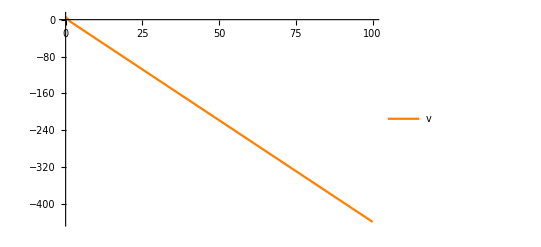

```mathematica
Plot[{Evaluate[v[x]/.Sol]},{x,x0,ℓ/2},PlotRange->All,PlotStyle->{Orange},PlotLegends->{"v"},PlotRange->All]
```

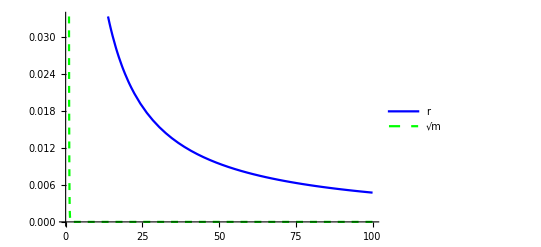

```mathematica
Plot[{Evaluate[r[x]/.Sol],Evaluate[m[v[x]]^(1/3)/.Sol]},{x,x0,ℓ/2},PlotStyle->{Blue,{Dashed,Green}},PlotLegends->{"r","√m"}]
```

```mathematica
rmax=100;
Action=Sqrt[r^2/(r^2-Subscript[m, 0]/r)+r^4 x'[r]^2];
A[ra_]:=2L(NIntegrate[Action/.NDSolve[{x'[r]==√(ra^4/(r^2(r^2-Subscript[m, 0]/r)(r^4-ra^4))),x[rmax]==0.01},x,{r,ra,rmax}],{r,ra,rmax}]-rmax)
q[ra_]:=2L*Abs[x[ra]/.NDSolve[{x'[r]==√(ra^4/(r^2(r^2-Subscript[m, 0]/r)(r^4-ra^4))),x[rmax]==0.01},x,{r,ra,rmax}]]
TherTable=Quiet[Partition[Flatten[Table[{q[ra],A[ra]},{ra,1,15,0.1}],2],2]];
TherRes=ListLinePlot[{TherTable},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Black,Dashed}];
VacRes=Plot[L(-(4Pi/q)(Gamma[3/4]/Gamma[1/4])^2),{q,0,60},PlotStyle->{Black, DotDashed},PlotRange->All];
```

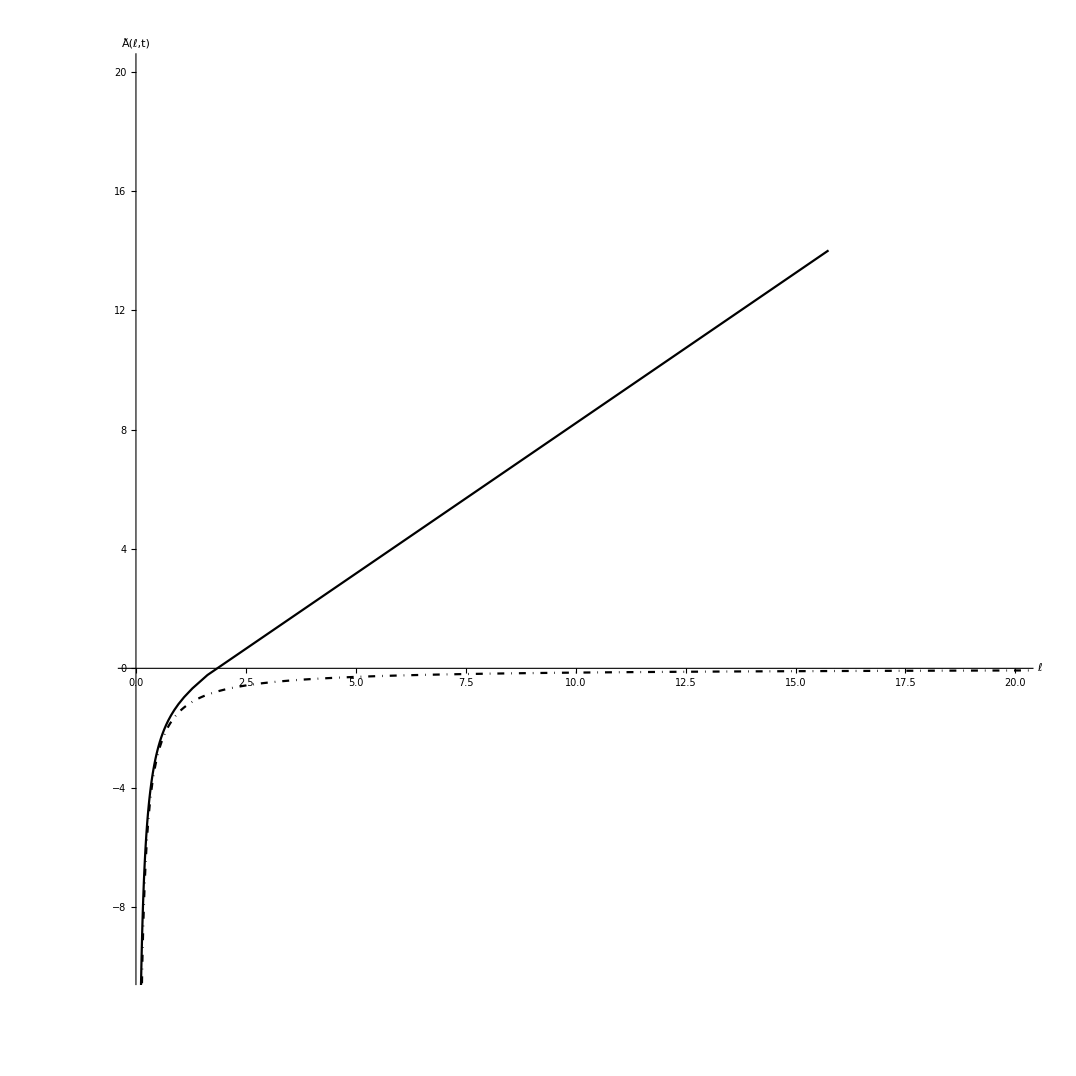

```mathematica
Show[{VacRes,TherRes},PlotRange->{{0,20},{-10,20}},AxesLabel->{"ℓ","Ã(ℓ,t)"},AspectRatio->1]
```

```mathematica
therin=Interpolation[TherTable,Method->"Hermite"]
therder=therin'
```

InterpolatingFunction[{{0.059733, 15.7508}}, <>]

InterpolatingFunction[{{0.059733, 15.7508}}, <>]

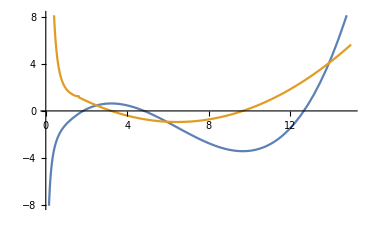

```mathematica
Plot[Evaluate[{therin[x],therder[x]}],{x,0.06,15}]
```

```mathematica
therder[15]
```

5.64798